# 1. Matrix-Vector Multiplication

We need to know how to get computers to build matrices and vectors and do all sorts of things to them.  Our matrices will mostly be real.

## Defining Matrices and Vectors

Random matrices are easy

```mathematica
{m,n}={6,5};
A=RandomReal[{-1,1},{m,n}];
b=RandomReal[{-1,1},n]
```

{-0.149062,-0.616088,-0.6545,0.407175,0.80849}

Typing in all the entries is a pain.

```mathematica
A={{1,2,3},{4,5,6},{7,8,9}};
b={11,12,13};
```

Importing things from the web (or anywhere else) is easy.

SparseArray[…]

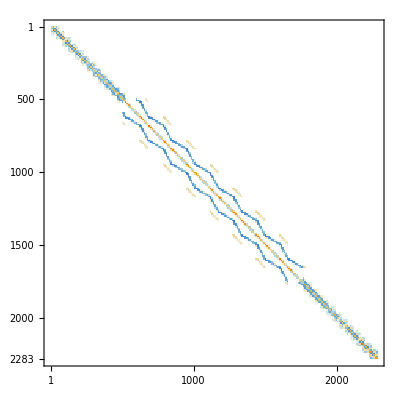

```mathematica
A=Import[
"https://math.nist.gov/pub/MatrixMarket2/SPARSKIT/fidap/fidap024.mtx.gz"]
MatrixPlot[A]
```

```mathematica
Max[A⟦1⟧]
```

Max[0,_]

## Multiplying Matrices and Vectors

In Mathematica a dot means matrix-vector and matrix-matrix multiplication

```mathematica
{m,n}={6,5};
A=RandomReal[{-1,1},{m,n}];
b=RandomReal[{-1,1},n];
A.b
```

{-0.290888,0.436782,0.405484,-0.0718737,0.464773,0.277624}

You get a warning if dimensions do not match!

```mathematica
{m,n}={6,5};
A=RandomReal[{-1,1},{m,n}];
b=RandomReal[{-1,1},m];
A.b
```

Dot::dotsh: Tensors {{0.978511,0.00401848,-0.455962,0.857208,0.133383},{-0.0575066,0.671616,-0.7471,-0.0839154,0.651934},{«1»},«1»,{«20»,«3»,-«20»},{-0.536815,0.290986,-0.457397,0.793876,-0.267434}} and {-0.350812,0.17792,0.341761,0.147543,0.0573384,0.0349564} have incompatible shapes.

{{0.978511,0.00401848,-0.455962,0.857208,0.133383},{-0.0575066,0.671616,-0.7471,-0.0839154,0.651934},{-0.740182,0.0335576,-0.312348,-0.242235,-0.533665},{-0.628,-0.0546641,-0.0140585,-0.183755,-0.55175},{0.309925,0.134769,0.0717391,-0.336111,-0.18112},{-0.536815,0.290986,-0.457397,0.793876,-0.267434}}.{-0.350812,0.17792,0.341761,0.147543,0.0573384,0.0349564}

It works the same for matrix-matrix multiplication

```mathematica
{m,n,r}={6,5,12};
A=RandomReal[{-1,1},{m,n}];
B=RandomReal[{-1,1},{n,r}];
Dimensions[A.B]
```

{6,12}

## Multiplying Matrices from scratch: Efficiency!

You can define matrix-matrix multiplication C=A.B from C_(i,j)=∑_k A_(i,k)B_(k,j) if you want but it is going to be slower (in every way you can imagine) than the built in command!

```mathematica
{m,n,r}={6,5,12};
A=RandomReal[{-1,1},{m,n}];
B=RandomReal[{-1,1},{n,r}];
CBuiltIn=A.B;
CFormula=Table[
Sum[A⟦i,k⟧B⟦k,j⟧,{k,n}],
{i,m},{j,r}];
Norm[CBuiltIn-CFormula]
```

0.

We can race the two versions!

```mathematica
{m,n,r}={6,5,12};
A=RandomReal[{-1,1},{m,n}];
B=RandomReal[{-1,1},{n,r}];
Timing[CBuiltIn=A.B;]
Timing[CFormula=Table[
Sum[A⟦i,k⟧B⟦k,j⟧,{k,n}],
{i,m},{j,r}];]
Norm[CBuiltIn-CFormula]
```

{0.,Null}

{0.,Null}

0.

## Assembling/Disassembling Matrices

We will frequently want to disassemble matrices and/or build matrices out of other matrices or vectors! For example, in the book we think of A is a bunch columns
	A=[a_1|a_2|…|a_n]

```mathematica
{m,n}={3,4};
A=RandomReal[{-1,1},{m,n}];
MatrixForm[A]
A⟦All,1⟧
A⟦1,All⟧
```

(-0.622226 | 0.12101 | 0.860154 | 0.501113
0.578527 | 0.419466 | 0.560189 | 0.727115
0.0768989 | 0.804953 | 0.398301 | -0.296475)

{-0.622226,0.578527,0.0768989}

{-0.622226,0.12101,0.860154,0.501113}

The book encourages us to think of 
	C=A.B=[A.b_1|A.b_2|…]
We can check this as follows

```mathematica
{m,n,r}={3,2,4};
A=RandomReal[{-1,1},{m,n}];B=RandomReal[{-1,1},{n,r}];
CBuiltIn=A.B;
CCols=Table[A.B⟦All,j⟧,{j,r}]ᵀ;
Map[MatrixForm,{CBuiltIn,CCols}]
```

{(-0.538761 | -0.529451 | 0.216178 | -0.182913
-1.04352 | -1.00425 | 0.284949 | -0.145691
-0.406725 | -0.363615 | -0.0639878 | 0.21619),(-0.538761 | -0.529451 | 0.216178 | -0.182913
-1.04352 | -1.00425 | 0.284949 | -0.145691
-0.406725 | -0.363615 | -0.0639878 | 0.21619)}

We can race the two versions!

```mathematica
{m,n,r}={3,2,4};
A=RandomReal[{-1,1},{m,n}];B=RandomReal[{-1,1},{n,r}];
Timing[CBuiltIn=A.B;]
Timing[CCols=Table[A.B⟦All,j⟧,{j,r}]ᵀ;]
Norm[CBuiltIn-CCols]
```

{0.,Null}

{0.,Null}

0.

## Block Matrices and Blocks of Matrices

A block matrix 
	A=(A_11 | A_12
A_21 | A_22
A_31 | A_33)
simply slams matrices (of matching dimensions) together.

```mathematica
{m,n}={2,3};
{{A11,A12},
{A21,A22},
{A31,A32}}=RandomReal[{-1,1},{3,2,m,n}];
A=ArrayFlatten[{{A11,A12},{A21,A22},{A31,A32}}];
Dimensions[A];
Map[MatrixForm,{A,A31}]
```

{(0.259097 | -0.693741 | -0.464709 | 0.00780268 | 0.0308603 | -0.739562
0.631357 | -0.873049 | 0.754059 | -0.55847 | 0.637892 | 0.270873
0.627391 | -0.00475637 | -0.126895 | -0.898593 | -0.603509 | 0.190056
0.923748 | -0.0803875 | 0.575368 | -0.243507 | -0.457498 | -0.154441
0.736949 | 0.168749 | 0.702667 | 0.329765 | 0.905742 | 0.529587
0.616778 | -0.948189 | -0.0277749 | -0.446024 | 0.4288 | -0.216694),(0.736949 | 0.168749 | 0.702667
0.616778 | -0.948189 | -0.0277749)}

You can grab a chunk of a matrix using the range notation

```mathematica
Map[MatrixForm,{A[[1;;m,1;;n]],A11}]
```

{(0.259097 | -0.693741 | -0.464709
0.631357 | -0.873049 | 0.754059),(0.259097 | -0.693741 | -0.464709
0.631357 | -0.873049 | 0.754059)}

## Inverse Matrices and Linear Solves

Almost all random square matrices A have an inverse A^-1 satisfying A^-1.A=Id

```mathematica
m=3;
A=RandomReal[{-1,1},{m,m}];
AInv=Inverse[A];
Norm[A.AInv-IdentityMatrix[m]]
```

2.22045×10^-16

Most of the time you do not want the inverse! You just want to solve the system A.x=b

```mathematica
m=3;
A=RandomReal[{-1,1},{m,m}]; b=RandomReal[{-1,1},m];
Timing[AInv=Inverse[A]; bSlow=AInv.b;]
Timing[bFast=LinearSolve[A,b];]
Norm[bSlow-bFast]
```

{0.,Null}

{0.,Null}

6.28037×10^-16